```mathematica
Clear["Global`*"]
$Assumptions = True;
```

# Differential equations

Consider the model:

```mathematica
mdl={deqn=y'[x]==k y[x],bnd=y[0]==y0};
```

```mathematica
$Assumptions=k>0&&y0>0;
```

Solution:

```mathematica
sln = DSolve[mdl,y[x],x]
```

{{y[x]→ⅇ^(k x) y0}}

```mathematica
y[x_]=y[x]/.sln[[1]];
```

Verify the solution:

```mathematica
deqn//FullSimplify
```

True

```mathematica
bnd//FullSimplify
```

True

Define values for the constants:

```mathematica
k=1; y0=1;
y[x]
```

ⅇ^x

```mathematica
dy[x_]=y'[x]
```

ⅇ^x

```mathematica
ddy[x_]=y''[x]
```

ⅇ^x

```mathematica
Roots[ddy[x]==0,x]
```

Roots::neq: ⅇ^x is expected to be a polynomial in the variable x.

Roots[ⅇ^x==0,x]

Plot the solution:

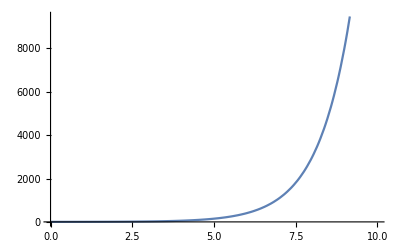

```mathematica
Plot[y[x],{x,0,10}]
```